```mathematica
<<Geometry`
```

## TEST1

### Case 1

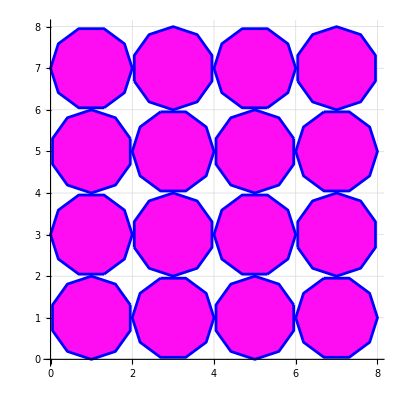

```mathematica
teil[figke_]:= Module[{rotp},
rotp=2mid[figke];
{figke,rot3[figke,{π/2,rotp}],rot3[figke,{π,rotp}],rot3[figke,{3 π /2,rotp}]}]
dpoly:={{{1,{{4,0},{4,5},{2,5},{2,4}}},{LightGreen,1}},{Green,1,.005,2 π,2 π}}
dpoly:={tra3[newGeo[10,RGBColor[1,.05,.95,.1]][[1]],{1,1}],{Blue,1,.005,2 π,2 π}}
Nest[teil,dpoly,2]//toGL//gr1
```

### Case 2

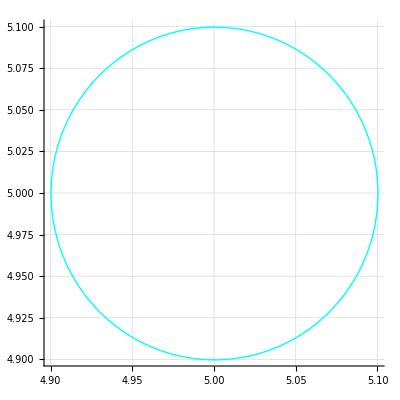

```mathematica
cCircle[{5,5},.1]//toGL//gr1
```

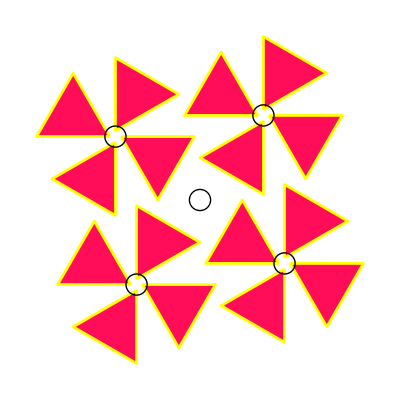

```mathematica
teil[figke_]:= Module[{rotp},
rotp=2mid[figke];
{figke,rot3[figke,{π/2,rotp}],rot3[figke,{π,rotp}],rot3[figke,{3 π /2,rotp}],
repCol[cCircle[rotp,.25],{Black}]
}]
dpoly:={{{1,{{4,0},{4,5},{2,5},{2,4}}},{LightGreen,1}},{Green,1,.005,2 π,2 π}}
dpoly:={tra3[newGeo[3,RGBColor[1,.05,.35,.1]][[1]],{1,1}],{Yellow,1,.005,2 π,2 π}}
Nest[teil,dpoly,2]//toGL//gr
```

### Case 3

```mathematica
ind:=Tuples[Composition@@{sym4ref,sym4rot,sym4ovr},2]
```

```mathematica
dpoly:={{{1,{{0,0},{0.5,0.2},{1,1},{0.2,0.9}}},{RGBColor[1, 0.9500000000000001, 0],1}},{RGBColor[0.06, 0.06, 0.06],1,0.005,2 π,2 π}}
dpoly:={{{1,{{0,0},{1,0},{0.7,1},{0.3,1}}},{RGBColor[0.87, 0.87, 0.87, 0.9],1}},{RGBColor[0.06, 0.06, 0.06],1,0.005,2 π,2 π}}
dpoly:={{{1,{{0,0},{0.5,0.5},{1.0,0.25}}},{RGBColor[0.87, 0.87, 0.87, 0.9],1}},{RGBColor[0.06, 0.06, 0.06],1,0.005,2 π,2 π}}
```

```mathematica
Table[ind[[k]][dpoly]//toGL//gr,{k,1,Length[ind]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}